# 几何区域上的 数值偏微分方程

## Wolfram 语言专题讲座系列

# -Graphics3D--Graphics3D--Graphics--Graphics3D--Graphics3D-

杨圣汇 Wolfram Research, Inc.

## 概述

几何区域上的偏微分方程数值解

微分算子的特征根和特征函数

视频链接

https://www.bilibili.com/video/BV1Af4y1e7cy

## 在几何区域上的偏微分方程数值解

## NDSolve

#### 求解偏微分方程

```mathematica
uif=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==10,u[x,0]==0,u[x,1]==1},u,{x,0,1},{y,0,1}]
```

#### 可视化结果

```mathematica
Plot3D[uif[x,y],{x,0,1},{y,0,1}]
```

## 如何求解偏微分方程

#### Wolfram 语言来描述问题

{x,y,..}∈Ω 定义域

PDE 方程本身

Γ 边界以及边界条件

## NDSolve

#### 建立对于问题的精确描述

```mathematica
Ω=Disk[];
```

```mathematica
op=-Laplacian[u[x,y],{x,y}]-1;
```

```mathematica
Subscript[Γ, D]=DirichletCondition[u[x,y]==0,x≥0];
```

#### 求解方程

```mathematica
uif=NDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈Ω];
```

#### 可视化

```mathematica
Plot3D[uif[x,y],{x,y}∈Ω]
```

## 特定 PDEs

系数形式 :                      d∂/(∂t)u+∇·(-c∇u-α u+γ)+β·∇u+a u=f

拉普拉斯:                                          ∇·(-c∇u-α u+γ)+β·∇u+a u=0

泊松:                                                   ∇·(-c∇u-α u+γ)+β·∇u+a u=f

荷姆霍兹:                                          ∇·(-c∇u -α u+γ)+β·∇u+a u=f

对流:                                                   ∇·(-c∇u-α u+γ)+β·∇u+a u=f

传热:                                      ∂/(∂t)u+∇·(-c∇u-α u+γ) +β·∇u+a u=f

波动:                      ∂^2/(∂t^2)u+∂/(∂t)u+∇·(-c∇u-α u+γ)+β·∇u+a u=0

偏微分方程系统

## 泊松方程

#### PDE

```mathematica
泊松形式:      ∇·(-c∇u-α u+γ)+β·∇u+a u=f
```

#### Dirichlet 边界条件

h u= r  on  ∂Ω

Ω

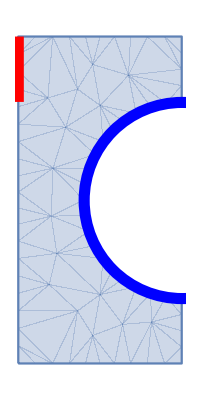

## 泊松方程

#### 建立问题的WL描述

```mathematica
Ω=ImplicitRegion[0≤x≤5&&0≤y≤10&&!((x-5)^2+(y-5)^2≤3^2),{x,y}];
```

```mathematica
op=-Laplacian[u[x,y],{x,y}]-20;
```

```mathematica
Subscript[Γ, D]={DirichletCondition[u[x,y]==0,x==0&&8≤y≤10],
DirichletCondition[u[x,y]==100,((x-5)^2+(y-5)^2==3^2)]};
```

#### 求解方程

```mathematica
uif=NDSolveValue[{op==0,Subscript[Γ, D]}, u,{x,y}∈Ω];
```

#### 可视化

```mathematica
Plot3D[uif[x,y],{x,y}∈Ω]
```

## 边界

#### Dirichlet 边界条件

h u= r  on  ∂Ω

#### 广义 Neumann 边界条件

n⃗·(c ∇u + α u - γ)= g - q u  on  ∂Ω

n⃗·(c ∇u + α u - γ)= 0  on  ∂Ω

#### 周期性边界条件

(a+b u)_(∂Ω_1)=u_(∂Ω_2)

## 泊松方程

h u=r  on  ∂Ω

```mathematica
Subscript[Γ, D]=DirichletCondition[u[x,y]==0,x==0&&8≤y≤10];
```

n⃗·(c ∇u + α u - γ)= g - q u  on  ∂Ω

```mathematica
Subscript[Γ, N]=NeumannValue[-2u[x,y],((x-5)^2+(y-5)^2==3^2)];
```

```mathematica
uif=NDSolveValue[{op==Subscript[Γ, N],Subscript[Γ, D]},u,{x,y}∈Ω];
```

```mathematica
Show[
Plot3D[uif[x,y],{x,y}∈uif["ElementMesh"],Mesh->None],
Graphics3D[{Opacity[0.2],EdgeForm[Gray],FaceForm[None],ElementMeshToGraphicsComplex[uif["ElementMesh"],"CoordinateConversion"->(Join[#,ConstantArray[{0.},{Length[#]}], 2]&)]}]
,ImageSize->Large]
```

## 边界条件理论

Dirichlet (蓝色部分) / Neumann 值 (绿色部分)

h u= r  on  ∂Ω
n⃗·(c ∇u + α u - γ)= g - q u  on  ∂Ω

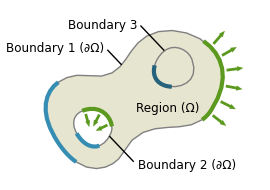

```mathematica
DirichletCondition[u[x,y..]==r,pred]
```

```mathematica
NeumannValue[g-q*u,pred]
```

## 原理 - NeumannValues

PDE + Neumann 条件 (蓝色):

∇·(-c ∇u -α u + γ ) +β·∇u + a u -f=0
n⃗·(c ∇u +α u - γ )= g - q u

FEM 推导:

∫_Ω ∇·(-c ∇u-α u+γ) ϕ+β·∇u ϕ+a u ϕ-f ϕⅆx=0

由部分积分可得:

∫_Ω (c ∇u+α u-γ) ·∇ϕ+β·∇u ϕ+a u ϕ-f ϕ ⅆx - ∫_(∂Ω) n⃗·(c ∇u+α u-γ)ϕⅆx=0

用 Neumann 条件替换并且可以得到:

∫_Ω (c ∇u+α u-γ) ·∇ϕ+β·∇u ϕ+a u ϕ-f ϕ ⅆx = ∫_(∂Ω) (g-q u) ϕⅆx

## 周期性边界条件

#### 描述问题

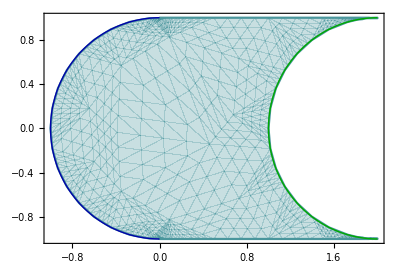

```mathematica
Ω=RegionDifference[RegionUnion[Disk[],Rectangle[{0,-1},{2,1}]],Disk[{2,0}]];
op=-∇_{x,y}^2 u[x,y]-If[(x-1/4)^2+y^2≤1/4,1,0];
```

## 周期性边界条件

#### 问题描述

(g+h u)_(f(pred))=u_pred

-Graphics-

```mathematica
pbc=PeriodicBoundaryCondition[u[x,y],x^2+y^2==1,Function[x,x+{2,0}]];
```

```mathematica
Show[RegionPlot[Ω],ContourPlot[(x)^2+y^2==1,{x,-1,0},{ y,-1,1}, ContourStyle->{Darker[Blue]},ColorFunction->Automatic],ContourPlot[(x-2)^2+y^2==1,{x,0.5,2},{ y,-1,1}, ContourStyle->{Darker[Green]},ColorFunction->Automatic]]
```

```mathematica
Subscript[Γ, Dc]=DirichletCondition[u[x,y]==0,(0<x<2&&(y==-1||y==1))];
```

## 周期性边界条件

#### 求解和可视化

```mathematica
ufun=NDSolveValue[{op==0,pbc,Subscript[Γ, Dc]},u,{x,y}∈Ω];
```

```mathematica
cp=ContourPlot[ufun[x,y],{x,y}∈Ω,ColorFunction->"TemperatureMap",AspectRatio->Automatic];
Show[
MapAt[Translate[#,{-2.2,0}]&,cp,1],
MapAt[Translate[#,{2.0,0}]&,cp,1],cp,
ToBoundaryMesh[ufun["ElementMesh"]]["Wireframe"],PlotRange->All]
```

## 瞬态解

#### 构建几何区域

```mathematica
Ω=ImplicitRegion[y≥0&&(x-3/2)^2+y^2≥1/25&&x^2+y^2≥ 1&&x^2+y^2≤4&&y≤x Tan[π/8],{x,y}];
```

## 瞬态解

#### 构建拉普拉斯算子和边界条件

```mathematica
top[t_,x_,y_]:=-10 ∇_{x,y}^2 u[t,x,y];
```

```mathematica
Subscript[Γ, Dc][t_]={DirichletCondition[u[t,x,y]==200.,x^2+y^2==1],
DirichletCondition[u[t,x,y]==15.,x^2+y^2==4]};
```

```mathematica
Subscript[Γ, Nv][t_]=NeumannValue[If[t≤10.,-100.t,-1000.],(x-3/2)^2+y^2==1/25];
```

## 瞬态解

#### 求解

```mathematica
uinit=NDSolveValue[{top[0,x,y]==0,Subscript[Γ, Dc][0]},u[0,x,y],{x,y}∈Ω];
```

```mathematica
mesh=Head[uinit]["ElementMesh"];
uif=NDSolveValue[{D[u[t,x,y],t]+top[t,x,y]==Subscript[Γ, Nv][t],Subscript[Γ, Dc][0],u[0,x,y]==uinit},u,{t,0,25},{x,y}∈mesh];
```

#### 可视化

```mathematica
framesNTV=Table[ContourPlot[uif[t,x,y],{x,y}∈mesh,Mesh->None,Contours->21,PlotRange->All,Frame->False],{t,1/2,15,1/2}];
ListAnimate[framesNTV,SaveDefinitions->True]
```

## 瞬态解

#### 可视化结果

```mathematica
cp=ContourPlot[uif[25,x,y],{x,y}∈mesh,Mesh->None,Contours->21,PlotRange->All,Frame->False];
```

```mathematica
Show[{Graphics[{Circle[{0,0},2],Circle[{0,0},1],Circle[#,1/5]&/@{{-1,-1},{-1,1},{1,-1},{1,1},{3/2,0},{-3/2,0},{0,3/2},{0,-3/2}}},PlotRange->{{0.7,2.2},{-0.5,1}}],cp}]
```

## 波动方程

```mathematica
∂^2/(∂t^2)u+∂/(∂t)u+ ∇·(-c ∇u -α u + γ) +β·∇u + a u = 0
```

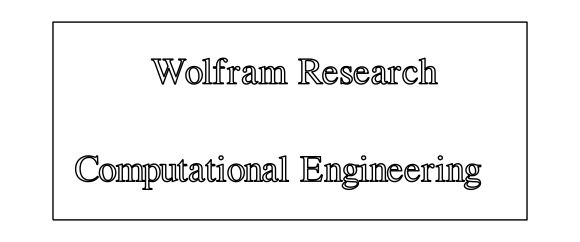

POV-Ray 渲染

Ca. 50,000 elements, compute time ca. 5 minutes, render time ca. 5 hours.

## 波动方程的边界条件

u_tt==u_xx

(u_t | == | v
v_t | == | u_xx)

## 反射边界

#### 方程式描述

```mathematica
refl=D[u[t,x],{t,2}]-Laplacian[u[t,x],{x}];
```

```mathematica
init[x_]=D[0.125 Erf[(x-0.5)/0.125],x];
ic={u[0,x]==init[x],Derivative[1,0][u][0,x]==0};
```

#### 求解以及可视化

```mathematica
ufun=NDSolveValue[{refl==0,ic},u,{t,0,1},{x,0,1},Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}];
```

```mathematica
list=Table[Plot[ufun[t,x],{x,0,1},PlotRange->{-0.1,1.3}],{t,0,1,0.1}];
ListAnimate[list]
```

## 吸收振动的边界

#### 问题设定

```mathematica
absorb=refl+NeumannValue[Derivative[1,0][u][t,x],x==0||x==1];
```

#### 求解方程和可视化

```mathematica
ufun=NDSolveValue[{absorb==0,ic},u,{t,0,1},{x,0,1},Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}];
```

```mathematica
list=Table[Plot[ufun[t,x],{x,0,1},PlotRange->{-0.1,1.3}],{t,0,1,0.1}];
ListAnimate[list]
```

## 吸收振动的边界

#### 问题设定

```mathematica
ic={u[0,x]==init[x],Derivative[1,0][u][0,x]==-D[init[x],x]};
```

```mathematica
bc=PeriodicBoundaryCondition[u[t,x],x==0,TranslationTransform[{1}]];
```

#### 求解方程并可视化

```mathematica
ufun=NDSolveValue[{absorb==0,ic,bc},u,{t,0,2},{x,0,1},Method->"MethodOfLines"];
```

```mathematica
plots=Table[Plot[ufun[t,x],{x,0,1},PlotRange->{-0.1,1.3}],{t,0,2,.1}];
ListAnimate[plots]
```

## n 偏微分方程系统

以下是两个偏微分方程，其中u 和 v 为独立变量

∇·(-c_11∇u-c_12∇v-α_11 u+α_12 v+γ_1)+β_11·∇u+β_12·∇v+a_11 u+a_12 v ==f_1
∇·(-c_21∇u-c_22∇v-α_21 u+α_22 v+γ_2)+β_21·∇u+β_22·∇v+a_21 u+a_22 v==f_2

#### Dirichlet 条件

h_11 u+h_21 v=r_1
h_21 u+h_22 v=r_2

#### 广义 Neumann 条件

n⃗·(c_11 ∇u +c_12∇v)= g_1 - q_11 u - q_12 v 
n⃗·(c_21 ∇u +c_22∇v)= g_2 - q_21 u - q_22 v

## 斯托克斯流

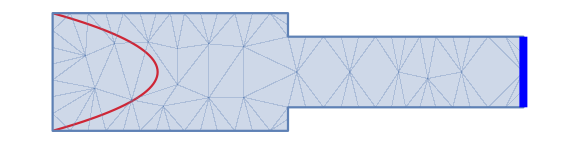

(({{-1,0},{0,-1}}.u[x,y]{x,y}Inactive){x,y}Inactive+p^(1,0)[x,y]==0
({{-1,0},{0,-1}}.v[x,y]{x,y}Inactive){x,y}Inactive+p^(0,1)[x,y]==0
v^(0,1)[x,y]+u^(1,0)[x,y]==0)

## 斯托克斯流

#### 程序描述

```mathematica
Ω=ImplicitRegion[0≤x≤2&&0≤y≤0.5&&!(x≥1&&y≤0.1)&&!(x≥1&&y≥0.4),{x,y}];
```

```mathematica
pde=StokesFlow[1,{u[x,y],v[x,y],p[x,y]},{x,y}]=={0,0,0};
```

```mathematica
Subscript[Γ, D]={DirichletCondition[u[x,y]==4*0.3*y*(0.5-y)/(0.41)^2,x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<x<2],DirichletCondition[p[x,y]==0.,x== 2]};
```

## 斯托克斯流

#### 方程求解

```mathematica
{xVel,yVel,pressure}=NDSolveValue[{pde,Subscript[Γ, D]},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}];
```

#### 可视化

```mathematica
Show[RegionPlot[Ω],VectorPlot[{xVel[x,y], yVel[x,y]},{x,y}∈Ω,StreamPoints->6,StreamColorFunction->"TemperatureMap",StreamColorFunctionScaling->False]//Quiet]
```

## 3D 机械结构

曲轴两端固定，活塞挤压曲轴发生形变

```mathematica
gr=-Graphics3D-;
```

#### 依据问题建立程序

```mathematica
mesh=ToElementMesh[DiscretizeGraphics[gr],"MeshOrder"->1]
```

```mathematica
Y=10^9;
ν=33/100;
pde=Stress[{Y,ν},{u[x,y,z],v[x,y,z],w[x,y,z]},{x,y,z}]== {0,0,NeumannValue[-10000.,((217≤y≤256)&&(40≤z≤103))||((584≤y≤622)&&(40≤z≤103))]};
```

```mathematica
Subscript[Γ, D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==0.},{y≤0.1,y≥890}]};
```

## 3D 机械结构

#### 求解方程

```mathematica
AbsoluteTiming[
{uif,vif,wif}=NDSolveValue[{pde,Subscript[Γ, D]}, {u,v,w},{x,y,z}∈mesh];]
```

#### 可视化

```mathematica
Show[
ToBoundaryMesh[mesh]["Wireframe"["MeshElementStyle"->{Directive[EdgeForm[],FaceForm[Gray]]}]],
ElementMeshDeformation[mesh,{uif,vif,wif},"ScalingFactor"->100]["Wireframe"[AspectRatio->Automatic,"MeshElementStyle"->Directive[EdgeForm[],FaceForm[Red]]]]
]
```

## 数值特征根问题

## 特征根问题

PDE

∇·(-c∇u -α u+γ)+β·∇u+a u=λ u

{x,y,..}∈Ω

Γ

## NDEigensystem

-∇_x^2 u =λ u

```mathematica
{vals,funs}=NDEigensystem[-Laplacian[u[x],{x}],u[x],{x,0,π},4];
```

```mathematica
vals
```

```mathematica
Plot[funs,{x,0,π}]
```

## NDEigensystem

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],6];
```

```mathematica
vals
```

```mathematica
Table[Plot3D[funs[[i]],{x,y}∈Disk[],PlotRange->All,PlotLabel->vals[[i]],PlotTheme->"Minimal"],{i,Length[vals]}]
```

## NDEigensystem

```mathematica
img = Import["http://upload.wikimedia.org/wikipedia/commons/d/d3/Mini_cross_section.jpg"];
```

Mask tool → boundary graphics.

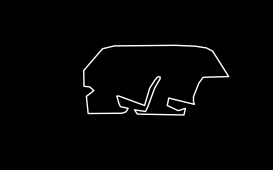
```mathematica
boundary=-Graphics-;
```

## NDEigensystem

```mathematica
bdr=BoundaryDiscretizeGraphics[boundary]
```

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x,y],{x,y}]},u[x,y],{x,y}∈bdr,6];
```

## NDEigensystem

```mathematica
Show[img,ContourPlot[funs[[2]],{x,y}∈bdr,Axes->None,Frame->None,AspectRatio->Automatic,ColorFunction->Function[f,{Opacity[0.75],ColorData["TemperatureMap"][f]}]],ImageSize->Automatic]
```

## 数值偏微分方程求解

#### 总结

线性变量系数

瞬时状态

特征根和特征函数

在任意几何区域上的一维，二维和三维偏微分方程

## 感谢各位参加线上活动！

## 初始化

```mathematica
Needs["NDSolve`FEM`"]
$HistoryLength=0;
SetOptions[#,{ColorFunction->"TemperatureMap",AspectRatio->Automatic}]& /@{ContourPlot,DensityPlot};
SetOptions[RegionPlot,AspectRatio->Automatic];
SetOptions[#,{ColorFunction->"TemperatureMap",AspectRatio->Automatic,Boxed->False,Axes->False}]&/@{Plot3D};
```

```mathematica
ClearAll[insertMaterial]
insertMaterial[val_,p_Piecewise]:=Module[{materialRules,conditions,defaultMaterialRule},materialRules=p[[1,All,1]];
conditions=Join[p[[1,All,2]],{True}];
defaultMaterialRule=p[[2]];
Internal`ToPiecewise[conditions,Join[val/.materialRules,{val/.defaultMaterialRule}],False]]


ClearAll[mkRulePiecewise]
mkRulePiecewise[ruleLhs:{__Symbol},a_List]:=MapThread[Rule,{ruleLhs,a}]
mkRulePiecewise[ruleLhs:{__Symbol},p_Piecewise]:=Module[{conditions,rules},conditions=Join[p[[1,All,2]],{True}];
rules=MapThread[Rule,{ruleLhs,#}]&/@Join[p[[1,All,1]],{p[[2]]}];
Internal`ToPiecewise[conditions,rules,False]]

ClearAll[mkMaterialDispatcher]
mkMaterialDispatcher[ruleLhs:{__Symbol},input_]:=Block[{newPW},newPW=mkRulePiecewise[ruleLhs,input];
If[Head[newPW]===List,With[{newPW=newPW},Function[in,in/.newPW]],With[{newPW=newPW},Function[in,insertMaterial[in,newPW]]]]]
```

```mathematica
Stress[{Y_,nu_},U:{u_,v_,w_},X:{x_,y_,z_}]:=With[{res=Catch[iStress[PiecewiseExpand[Piecewise[{{{Y,nu},True}}]],U,X,Stress],NDSolve`FEM`FEMError[___]]},res/;Unevaluated[res]=!=$Failed]

ClearAll[iStress];
iStress[a_,{u_,v_,w_},X:{x_,y_,z_},msghead_Symbol]/;(Head[a]==List&&Length[a]==2)||Head[a]==Piecewise:=Module[{pStress,Y,nu,valF},pStress=-{{{{((1-nu)*Y)/((1-2*nu)*(1+nu)),0,0},{0,Y/(2*(1+nu)),0},{0,0,Y/(2*(1+nu))}},{{0,(nu*Y)/((1-2*nu)*(1+nu)),0},{Y/(2*(1+nu)),0,0},{0,0,0}},{{0,0,(nu*Y)/((1-2*nu)*(1+nu))},{0,0,0},{Y/(2*(1+nu)),0,0}}},{{{0,Y/(2*(1+nu)),0},{(nu*Y)/((1-2*nu)*(1+nu)),0,0},{0,0,0}},{{Y/(2*(1+nu)),0,0},{0,((1-nu)*Y)/((1-2*nu)*(1+nu)),0},{0,0,Y/(2*(1+nu))}},{{0,0,0},{0,0,(nu*Y)/((1-2*nu)*(1+nu))},{0,Y/(2*(1+nu)),0}}},{{{0,0,Y/(2*(1+nu))},{0,0,0},{(nu*Y)/((1-2*nu)*(1+nu)),0,0}},{{0,0,0},{0,0,Y/(2*(1+nu))},{0,(nu*Y)/((1-2*nu)*(1+nu)),0}},{{Y/(2*(1+nu)),0,0},{0,Y/(2*(1+nu)),0},{0,0,((1-nu)*Y)/((1-2*nu)*(1+nu))}}}};

valF=mkMaterialDispatcher[{Y,nu},a];
{Inactive[Div][valF[pStress[[1,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[1,2]]].Inactive[Grad][v,X],X]+Inactive[Div][valF[pStress[[1,3]]].Inactive[Grad][w,X],X],Inactive[Div][valF[pStress[[2,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[2,2]]].Inactive[Grad][v,X],X]+Inactive[Div][valF[pStress[[2,3]]].Inactive[Grad][w,X],X],Inactive[Div][valF[pStress[[3,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[3,2]]].Inactive[Grad][v,X],X]+Inactive[Div][valF[pStress[[3,3]]].Inactive[Grad][w,X],X]}]
```

```mathematica
StokesFlow[mu_,depVars:{u_,v_,___,p_},X:{x_,y_,___}]/;Length[X]≥2&&Length[depVars]==Length[X]+1:=With[{res=Catch[iStokesFlow[PiecewiseExpand[Piecewise[{{mu,True}}]],depVars,X,StokesFlow],NDSolve`FEM`FEMError[___]]},res/;Unevaluated[res]=!=$Failed]

ClearAll[iStokesFlow];
iStokesFlow[a_,depVars:{u_,v_,___,p_},X:{x_,y_,___},msghead_Symbol]:=Module[{diag},diag=-a*IdentityMatrix[Length[depVars]-1];
Join[(Inactive[Div][diag.Inactive[Grad][#,X],X]&/@Most[depVars])+(D[p,#]&/@X),{Total[MapThread[D[#1,#2]&,{Most[depVars],X}]]}]]
```